## Statistics

### Random numbers

```mathematica
1
```

```mathematica
RandomInteger[]
```

0

```mathematica
2
```

```mathematica
RandomInteger[{-1,1}]
```

1

```mathematica
3
```

```mathematica
RandomInteger[{-1,1},7]
```

{-1,0,1,-1,-1,-1,1}

```mathematica
4
```

```mathematica
RandomInteger[{-10,10},{7,4}]
```

{{-9,-2,6,10},{5,10,3,-7},{7,-2,-4,10},{-1,-2,8,-6},{-10,9,3,0},{-4,-9,-2,5},{3,1,10,-5}}

```mathematica
5
```

```mathematica
RandomReal[]
```

0.946141

```mathematica
6
```

```mathematica
RandomComplex[]
```

0.411636+0.79253 ⅈ

```mathematica
7
```

```mathematica
RandomPrime[{1,100},6]
```

{43,11,61,83,61,79}

```mathematica
8
```

```mathematica
SeedRandom[6467789];RandomInteger[{-1,1},3]
```

{0,1,-1}

```mathematica
9
```

```mathematica
SeedRandom[Method->"MersenneTwister"];RandomInteger[{-1,1},{3,3}]//MatrixForm
```

(1 | -1 | 1
1 | 0 | 0
0 | -1 | -1)

```mathematica
10
```

```mathematica
SeedRandom[]
```

```mathematica
11
```

```mathematica
BlockRandom[RandomReal[1]]
```

0.943218

```mathematica
12
```

```mathematica
SeedRandom[121];{RandomReal[],BlockRandom[RandomReal[]],RandomReal[],RandomReal[]}
```

{0.0908251,0.194288,0.194288,0.296762}

### Random Sampling

```mathematica
13
```

```mathematica
SeedRandom[12345];
RanData=RandomReal[{0,1},10]
```

{0.121246,0.329922,0.782753,0.430168,0.223586,0.463053,0.738017,0.707618,0.790911,0.105714}

```mathematica
14
```

```mathematica
RandomChoice[RanData]
```

0.738017

```mathematica
15
```

```mathematica
RandomChoice[RanData,{3,1}]
```

{{0.329922},{0.738017},{0.223586}}

```mathematica
16
```

```mathematica
RandomChoice[RanData,5]
```

{0.790911,0.463053,0.329922,0.430168,0.329922}

```mathematica
17
```

```mathematica
RandomSample[RanData,9]
```

{0.105714,0.790911,0.463053,0.738017,0.707618,0.782753,0.430168,0.223586,0.329922}

```mathematica
18
```

```mathematica
W={0.03,0.08,0.22,0.04,0.12,0.3,0.12,0.03,0.04,0.02};
RandomChoice[W->RanData,2]
```

{0.223586,0.430168}

```mathematica
19
```

```mathematica
RandomSample[W->RanData,3]
```

{0.463053,0.738017,0.223586}

### Systematic Sampling

```mathematica
20
```

```mathematica
SeedRandom[09876]
RPrime=RandomPrime[{1,100},200];
Length[RPrime]
```

```mathematica
200
```

```mathematica
21
```

```mathematica
j=Length[RPrime]/20
```

```mathematica
10
```

```mathematica
22
```

```mathematica
RandomSample[Range[10],1]
```

```mathematica
{9}
```

```mathematica
23
```

```mathematica
RPrime
```

{17,11,67,97,11,73,71,61,71,31,59,29,79,7,71,89,79,11,2,29,97,61,2,71,3,79,31,83,83,17,37,89,41,31,61,7,11,53,17,61,71,2,53,23,29,59,11,41,13,71,3,53,13,61,19,2,17,17,59,3,11,41,83,59,41,47,13,59,17,5,5,59,79,37,97,7,11,23,41,83,67,79,73,73,73,41,79,17,59,37,83,71,73,17,2,11,41,89,97,7,2,23,13,67,79,83,5,61,47,73,61,97,53,53,2,89,19,19,61,89,83,43,73,3,83,17,5,89,29,23,7,23,53,97,2,83,13,17,37,2,19,59,79,29,43,19,7,43,59,47,3,41,23,53,37,59,29,83,37,59,19,59,31,89,2,67,47,47,97,2,47,97,41,11,43,37,7,59,67,83,89,2,17,13,2,7,73,83,89,2,3,59,17,19,73,13,53,29,89,83}

```mathematica
24
```

```mathematica
Table[9+n*j,{n,0,19}]
```

{9,19,29,39,49,59,69,79,89,99,109,119,129,139,149,159,169,179,189,199}

```mathematica
25
```

```mathematica
Table[RPrime[[9+n*j]],{n,0,19}]
```

{71,2,83,17,13,59,17,41,59,97,47,61,29,37,59,37,97,67,89,89}

```mathematica
26
```

```mathematica
MapAt[Style[#,FontColor->ColorData["HTML"]["Red"]]&,RPrime,{#}&/@{9,19,29,39,49,59,69,79,89,99,109,119,129,139,149,159,169,179,189,199}]
```

{17,11,67,97,11,73,71,61,71,31,59,29,79,7,71,89,79,11,2,29,97,61,2,71,3,79,31,83,83,17,37,89,41,31,61,7,11,53,17,61,71,2,53,23,29,59,11,41,13,71,3,53,13,61,19,2,17,17,59,3,11,41,83,59,41,47,13,59,17,5,5,59,79,37,97,7,11,23,41,83,67,79,73,73,73,41,79,17,59,37,83,71,73,17,2,11,41,89,97,7,2,23,13,67,79,83,5,61,47,73,61,97,53,53,2,89,19,19,61,89,83,43,73,3,83,17,5,89,29,23,7,23,53,97,2,83,13,17,37,2,19,59,79,29,43,19,7,43,59,47,3,41,23,53,37,59,29,83,37,59,19,59,31,89,2,67,47,47,97,2,47,97,41,11,43,37,7,59,67,83,89,2,17,13,2,7,73,83,89,2,3,59,17,19,73,13,53,29,89,83}

### Central tendency measures

```mathematica
27
```

```mathematica
List1=Table[Prime[i],{i,10}];
"Prime list :" <>ToString@ List1
"Mean: "<>ToString@Mean@N@List1
```

Prime list :{2, 3, 5, 7, 11, 13, 17, 19, 23, 29}

Mean: 12.9

```mathematica
28
```

```mathematica
"Median: "<>ToString@Median@List1
```

Median: 12

```mathematica
29
```

```mathematica
Counts[List1]
```

<|2→1,3→1,5→1,7→1,11→1,13→1,17→1,19→1,23→1,29→1|>

### Measures of dispersion

```mathematica
30
```

```mathematica
"Range: "<>ToString[Max[List1]-Min[List1]]
```

Range: 27

```mathematica
31
```

```mathematica
"Variance: "<>ToString[N[Variance[List1],3]]
```

Variance: 81.4

```mathematica
32
```

```mathematica
{"Square root of Variance: " <>ToString[N[Sqrt[Variance[List1]],2]],
"StandardDeviation: " <>ToString[N[StandardDeviation[List1],2]]}
```

{Square root of Variance: 9.0,StandardDeviation: 9.0}

```mathematica
33
```

```mathematica
z=N[(List1[[2]]-Mean@List1)/(StandardDeviation@List1),3];
"z score: " <> ToString@z
```

z score: -1.10

```mathematica
34
```

```mathematica
"Quartiles: " <> ToString@Quartiles[List1]
```

Quartiles: {5, 12, 19}

```mathematica
35
```

```mathematica
Quantile[List1,0.75]
```

19

```mathematica
36
```

```mathematica
InterquartileRange[List1]
```

14

### Statistical Charts

```mathematica
37
```

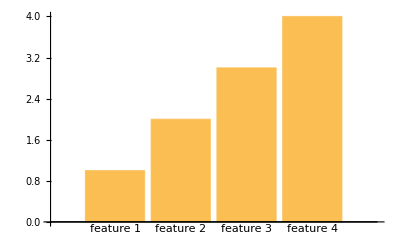

```mathematica
BarChart[{1,2,3,4},ChartLabels->{"feature 1","feature 2","feature 3","feature 4"}]
```

```mathematica
38
```

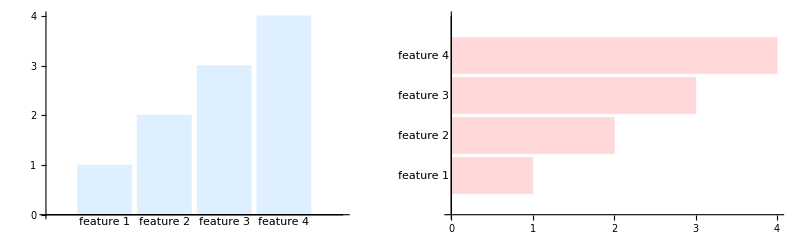

```mathematica
GraphicsRow[{BarChart[{1,2,3,4},ChartLabels->{"feature 1","feature 2","feature 3","feature 4"},BarOrigin->Bottom,ChartStyle->LightBlue],BarChart[{1,2,3,4},ChartLabels->{"feature 1","feature 2","feature 3","feature 4"},BarOrigin->Left,ChartStyle->LightRed]}]
```

```mathematica
39
```

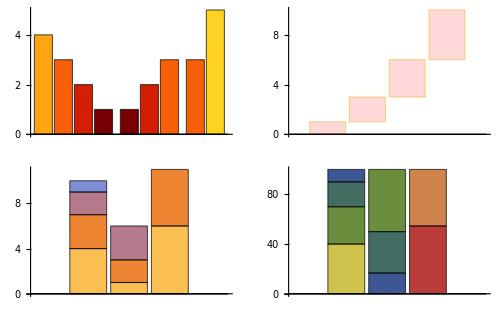
-Graphics-Bar Charts

```mathematica
Labeled[GraphicsGrid[
{{
BarChart[{{4,3,2,1},{1,2,3},{3,5}},ChartLayout->"Grouped",ColorFunction->"SolarColors"],
BarChart[{1,2,3,4},ChartStyle->LightRed,ChartLayout->"Stepped"]},
{BarChart[{{4,3,2,1},{1,2,3},{6,5}},ChartLayout->"Stacked"],
BarChart[{{4,3,2,1},{1,2,3},{6,5}},ChartLayout->"Percentile",ColorFunction->"DarkRainbow"]
}},Frame->All,FrameStyle->Directive[Black,Dashed],Background->LightBlue,ImageSize->500],"Bar Charts",Top]
```

```mathematica
40
```

```mathematica
SeedRandom[123]
Labeled[GraphicsGrid[
{{
BarChart3D[{{4,3,2,1},{1,2,3},{3,5}},ChartLayout->"Grouped",ColorFunction->"SolarColors"],
BarChart3D[{1,2,3,4},ChartStyle->LightRed,ChartLayout->"Stepped"]},
{BarChart3D[RandomReal[1,{10,5}],ChartLayout->"Stacked"],
BarChart3D[{{4,3,2,1},{1,2,3},{6,5}},ChartLayout->"Percentile",ColorFunction->"DarkRainbow"]
}},Frame->All,FrameStyle->Directive[Red,Thick],Background->LightBlue,ImageSize->500],"3D Bar Charts",Top,Frame->True,Background->White]
```

-Graphics-3D Bar Charts

```mathematica
41
```

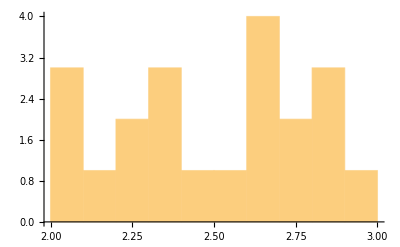

```mathematica
SeedRandom[4322]
hist1=Table[RandomReal[{2,3}],{i,0,20}];
Histogram[hist1,10]
```

```mathematica
42
```

```mathematica
hist2=Table[Cos[i],{i,1,20}];
hist3=Table[Sin[i],{i,1,10}];
GraphicsColumn[{Histogram[{hist1,hist2},10,BarOrigin->Left,ChartStyle->"Pastel",ChartLegends->{"rand num","Cos(x)"}],Histogram[{hist2,hist3},10,ChartLayout->"Overlapped",ChartStyle->"Pastel",ChartLegends->{"Cos(x)","Sin(x)"}],Histogram[{hist2,hist3},10,ChartLayout->"Stacked",ChartStyle->"Pastel",ChartLegends->{"Cos(x)","Sin(x)"}]}]
```

-Graphics-

```mathematica
43
```

```mathematica
SeedRandom[123]
GraphicsRow[{PairedHistogram[{RandomReal[{0,1},20]},{RandomReal[{0,1},20]},BarOrigin->Left],PairedHistogram[{RandomReal[{0,1},20]},{RandomReal[{0,1},20]},10,BarOrigin->Top,ChartStyle->"Pastel"]}]
```

-Graphics-

```mathematica
44
```

```mathematica
GraphicsRow[{PieChart[{1,1,1},ChartLegends->{"part a","part b","part c"},ChartStyle->{LightRed, LightBlue, LightYellow}],
PieChart[{1,1},ChartLegends->{"part a","part b"},ChartStyle->"SunsetColors"]}]
```

-Graphics-

```mathematica
45
```

```mathematica
SectorChart[{{2,1},{1,2}},ChartLegends->{"Sector a","Sector b"},ChartStyle->{LightRed, LightYellow}]
```

-Graphics-

```mathematica
46
```

```mathematica
GraphicsGrid[
{
{SectorChart3D[{{2,1,1},{3,1,2},{1,2,2}},PlotLabel->"3D Sector chart",ChartStyle->{Red, Blue,Yellow}],
PieChart3D[{1,1,1},ChartStyle->"GrayTones",PlotLabel->"3D Pie Chart"]},
{Histogram3D[Table[{i^3,i^-1},{i,20}],10,ChartElementFunction->"GradientScaleCube",PlotLabel->"3D Histogram"],""}
},ImageSize->500,Frame->True,FrameStyle->Directive[Thick,Dotted]]
```

-Graphics-

```mathematica
47
```

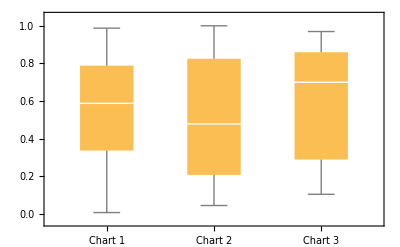

```mathematica
SeedRandom[1234]
BoxWhiskerChart[{Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,15}]},ChartLabels->{"Chart 1","Chart 2","Chart 3"}]
```

```mathematica
48
```

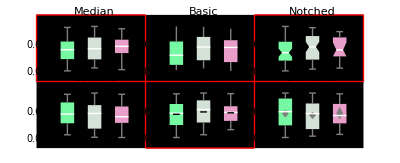

```mathematica
SeedRandom[123]
GraphicsGrid[{{BoxWhiskerChart[{Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,15}]},#,PlotLabel->Style[#,White],
ImageSize->Medium,ChartStyle->"MintColors",FrameStyle->Directive[White,12]]&["Median"],
BoxWhiskerChart[{Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,15}]},#,PlotLabel->Style[#,LightOrange],ImageSize->Medium,ChartStyle->"MintColors",FrameStyle->Directive[Orange,12]]&["Basic"],
BoxWhiskerChart[{Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,15}]},#,PlotLabel->Style[#,White],ImageSize->Medium,ChartStyle->"MintColors",FrameStyle->Directive[White,12]]}&["Notched"],
{BoxWhiskerChart[{Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,15}]},#,PlotLabel->Style[#,LightOrange],ImageSize->Medium,ChartStyle->"MintColors",FrameStyle->Directive[Orange,12]]&["Outliers"],
BoxWhiskerChart[{Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,15}]},#,PlotLabel->Style[#,White],ImageSize->Medium,ChartStyle->"MintColors",FrameStyle->Directive[White,12]]&["Mean"],
BoxWhiskerChart[{Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,50}],Table[RandomReal[],{i,0,15}]},#,PlotLabel->Style[#,LightOrange],ImageSize->Medium,ChartStyle->"MintColors",FrameStyle->Directive[Orange,12]]&["Diamond"]}},FrameTicksStyle->18,Frame->{None,None,{{1,1}->True,{2,2}->True,{1,3}->True}},FrameStyle->Directive[Thick,Red],Background->Black]
```

```mathematica
49
```

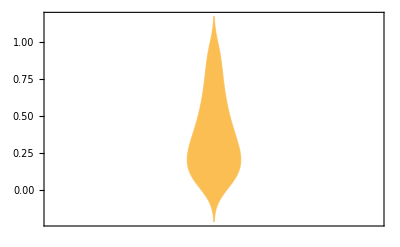

```mathematica
DistributionChart[Table[i^Exp[i],{i,0,1,0.01}]]
```

```mathematica
50
```

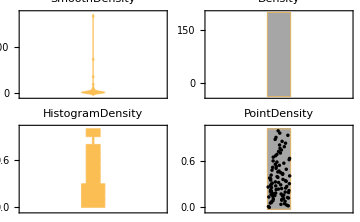

```mathematica
GraphicsGrid[{{DistributionChart[Table[i^Exp[i],{i,0,2,0.1}],ChartElementFunction->"SmoothDensity",PlotLabel->"SmoothDensity"],DistributionChart[Table[i^Exp[i],{i,1,2,0.1}],ChartElementFunction->"Density",PlotLabel->"Density",FrameStyle->Directive[Red,12]]},{DistributionChart[Table[i^Exp[i],{i,0,1,0.09}],ChartElementFunction->"HistogramDensity",PlotLabel->"HistogramDensity",FrameStyle->Directive[Red,12]],DistributionChart[Table[i^Exp[i],{i,0,1,0.0112}],ChartElementFunction->"PointDensity",PlotLabel->"PointDensity"]}},ImageSize->Medium,FrameStyle->Directive[Thickness[0.02],LightGray],Dividers->{2->Directive[Black,Dotted],2->Directive[Black,Dotted]},Frame->{1->False,False}]
```

```mathematica
51
```

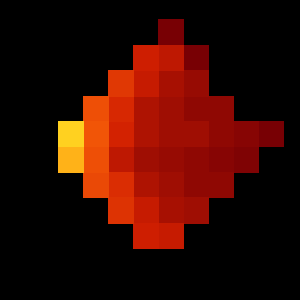

```mathematica
DensityHistogram[Flatten[Table[{x^2+y^2,x^2-y^2},{x,0,2,0.1},{y,0,2,0.1}],1],ChartBaseStyle->Red,ColorFunction->"SolarColors",Background->Black,FrameStyle->Directive[White,Thick],FrameLabel->{"X","Y"},ImageSize->300]
```

```mathematica
52
```

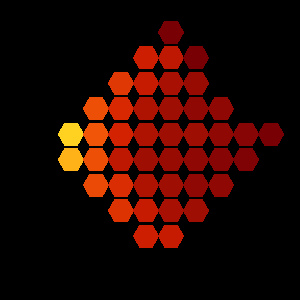

```mathematica
DensityHistogram[Flatten[Table[{x^2+y^2,x^2-y^2},{x,0,2,0.1},{y,0,2,0.1}],1],ChartBaseStyle->Red,ColorFunction->"SolarColors",Background->Black,FrameStyle->Directive[White,Thick],FrameLabel->{"X","Y"},ImageSize->300,ChartElementFunction->ChartElementDataFunction["Bubble","Shape"->"Hexagon"]]
```

```mathematica
53
```

```mathematica
Hist=Flatten[Table[{x^2+y^2,x^2-y^2},{x,0,2,0.1},{y,0,2,0.1}],1];
{MenuView[
{
DensityHistogram[Hist,Method->{"DistributionAxes"->True},ColorFunction->GrayLevel,ChartBaseStyle->Directive[FaceForm[Opacity[0.5]],EdgeForm[Red]],ChartLegends->BarLegend[Automatic,LegendMarkerSize->70],PlotLabel->Style[" Density Histogram 1", Bold],ChartElementFunction->#,ImageSize->200],
DensityHistogram[Hist,Method->{"DistributionAxes"->"Histogram"},ChartLegends->BarLegend[Automatic,LegendMarkerSize->70],PlotLabel->Style[" Density Histogram 2", Bold],ChartBaseStyle->EdgeForm[Thick],PlotTheme->"Scientific",ChartElementFunction->#,ImageSize->200],
DensityHistogram[Hist,Method->{"DistributionAxes"->"BoxWhisker"},ColorFunction->"BlueGreenYellow",PlotLabel->Style[" Density Histogram 3", Bold],ChartLegends->BarLegend[Automatic,LegendMarkerSize->70],ChartElementFunction->#,ImageSize->200]
}
]&[ChartElementDataFunction["Bubble","Shape"->"Hexagon"]],{
GraphicsRow[{
DensityHistogram[Hist,Method->{"DistributionAxes"->True},ColorFunction->GrayLevel,ChartBaseStyle->Directive[FaceForm[Opacity[0.5]],EdgeForm[Red]],ChartLegends->BarLegend[Automatic,LegendMarkerSize->70],PlotLabel->Style[" Density Histogram 1", Bold],ChartElementFunction->#,ImageSize->130],
DensityHistogram[Hist,Method->{"DistributionAxes"->"Histogram"},ChartLegends->BarLegend[Automatic,LegendMarkerSize->70],PlotLabel->Style[" Density Histogram 2", Bold],ChartBaseStyle->EdgeForm[Thick],PlotTheme->"Scientific",ChartElementFunction->#,ImageSize->130],
DensityHistogram[Hist,Method->{"DistributionAxes"->"BoxWhisker"},ColorFunction->"BlueGreenYellow",PlotLabel->Style[" Density Histogram 3", Bold],ChartLegends->BarLegend[Automatic,LegendMarkerSize->70],ChartElementFunction->#,ImageSize->130]
}&[ChartElementDataFunction["Bubble","Shape"->"Hexagon"]]]}}
```

{,{-Graphics-}}

### Ordinary Least Squares method

```mathematica
54
```

```mathematica
Data={{-1,10},{0,9},{1,7},{2,5},{3,4},{4,3},{5,0},{7,-1}};
Grid[Transpose[Prepend[Data,{"X","Y"}]],Dividers->{2->True,2->True},Alignment->Center]
```

X | -1 | 0 | 1 | 2 | 3 | 4 | 5 | 7
Y | 10 | 9 | 7 | 5 | 4 | 3 | 0 | -1

```mathematica
55
```

```mathematica
n=Length[Data];
SumX=Total@Data[[All,1]];
SumY=Total@Data[[All,2]];
SumXY=Total[Data[[All,1]]*Data[[All,2]]];
SumXSqre=Total@(Data[[All,1]]^2);
m=N@((n*SumXY-SumX*SumY)/(n*SumXSqre-Abs[SumX]^2));
b=N@((SumY*SumXSqre-SumX*SumXY)/(n*SumXSqre-Abs[SumX]^2));
```

```mathematica
56
```

```mathematica
Solve[SetPrecision[y==m*x+b,3],y]
```

{{y→8.47-1.47 x}}

```mathematica
57
```

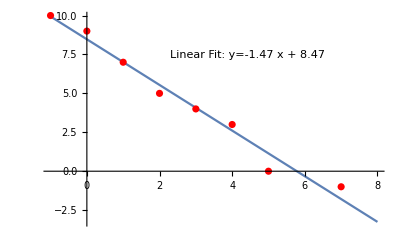

```mathematica
Show[Plot[b+m x,{x,-1,8},PlotLegends->Placed[" Linear Fit: y=-1.47 x + 8.47",{0.6,0.8}],PlotRange->Automatic],ListPlot[Data,PlotStyle->Red]]
```

```mathematica
58
```

```mathematica
r=N@((Covariance@@{Data[[All,1]],Data[[All,2]]})/(StandardDeviation@Data[[All,1]]*StandardDeviation@Data[[All,2]]))
```

-0.987814

```mathematica
59
```

```mathematica
N@Correlation[Data[[All,1]],Data[[All,2]]]
```

-0.987814

```mathematica
60
```

```mathematica
Model=LinearModelFit[Data,x,x,WorkingPrecision->10]
```

FittedModel[8.473684211-1.466165414 x]

```mathematica
61
```

```mathematica
{
"\n"Framed["Best Fit Parameters b and m: "<>ToString[Model["BestFitParameters" ]],Background->LightYellow],"\n"Framed["Equation: "<>ToString[Model["BestFit" ]],Background->LightYellow],
"\n"Framed["Pure Function: "<>ToString[SetPrecision[Model["Function" ],3]],Background->LightYellow],
"\n"Framed["r coeficcient: "<>ToString[r],Background->LightYellow]
}
```

{
 Best Fit Parameters b and m: {8.473684211, -1.466165414},
 Equation: 8.473684211 - 1.466165414 x,
 Pure Function: 8.47 - 1.47 #1 & ,
 r coeficcient: r}

```mathematica
62
```

```mathematica
Model["FitResiduals"]
```

{0.06015038,0.52631579,-0.0075188,-0.54135338,-0.07518797,0.39097744,-1.1428571,0.78947368}

```mathematica
63
```

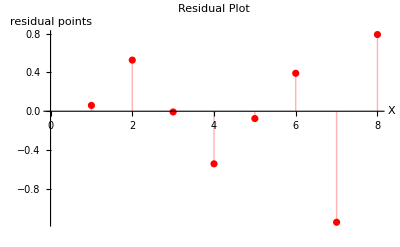

```mathematica
ListPlot[Model["FitResiduals"],PlotStyle->{Red,Thick},PlotLabel->"Residual Plot",AxesLabel->{Style["X",Bold],Style["residual points",Bold]},Filling->Axis]
```

```mathematica
64
```

```mathematica
Model["SinglePredictionConfidenceIntervalTable"]
```

Observed | Predicted | Standard Error | Confidence Interval
10 | 9.93984962 | 0.78481739 | {8.0194706,11.860229}
9 | 8.47368421 | 0.74856412 | {6.6420138,10.305355}
7 | 7.0075188 | 0.7228741 | {5.2387096,8.776328}
5 | 5.54135338 | 0.7088967 | {3.8067456,7.2759611}
4 | 4.07518797 | 0.70732661 | {2.3444221,5.8059538}
3 | 2.6090226 | 0.71824519 | {0.8515399,4.3665052}
0 | 1.1428571 | 0.74110068 | {-0.6705509,2.9562652}
-1 | -1.7894737 | 0.81811053 | {-3.791318,0.212371}

```mathematica
65
```

```mathematica
Model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 8.473684211 | 0.34167121 | 24.800697 | 2.8278226×10^-7
x | -1.466165414 | 0.094310214 | -15.5462 | 4.4832546×10^-6

```mathematica
66
```

```mathematica
Model["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
1 | 8.473684211 | 0.34167121 | {7.63764488,9.30972355}
x | -1.466165414 | 0.094310214 | {-1.69693419,-1.2353966}

```mathematica
67
```

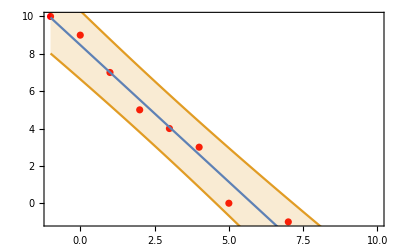

```mathematica
Model[x];
Model["SinglePredictionBands",ConfidenceLevel->0.95];
Show[
ListPlot[Data,PlotStyle->Red],
Plot[{Model[x],Model["SinglePredictionBands",ConfidenceLevel->0.95]},
{x,-1,10},Filling->{2->{1}}],PlotRange->{Automatic,{-1,10}},Frame->True,ImageSize->400]
```

```mathematica
68
```

```mathematica
Model["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 107.21335 | 107.21335 | 241.68432 | 4.48325×10^-6
Error | 6 | 2.6616541 | 0.44360902 |  | 
Total | 7 | 109.875 |  |  |